```mathematica
allPersClose = {0.00259494,0.00217527,0.00154131,0.00156934,0.00152773};
```

```mathematica
d = {0.05,0.04,0.03,0.02,0.01};
```

```mathematica
pStar = .84;
```

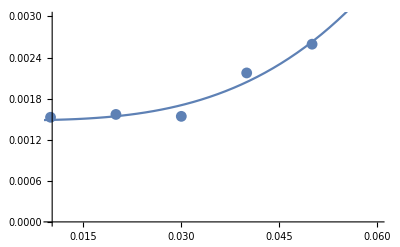

```mathematica
Show[
ListPlot[Table[{d[[i]],allPersClose[[i]]},{i,1,Length[allPersClose]}],
PlotRange->{{0.01,0.06},{0,0.003}}],
Plot[17.6280044 * x^3.21788679 + 0.00148272369, {x,0,0.06}]
]
```

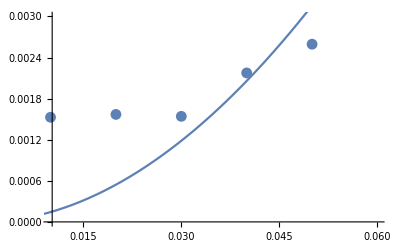

```mathematica
Show[
ListPlot[Table[{d[[i]],allPersClose[[i]]},{i,1,Length[allPersClose]}],
PlotRange->{{0.01,0.06},{0,0.003}}],
Plot[ x^1.92175769 , {x,0,0.06}]
]
```